## Te=3 keV Ti= 3keV ne=10^25cm^-3 α projectile: 001

### plotting dE/dx vs E from dedx.out file

```mathematica
st=OpenRead["dedx.001.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,Number]
proj=Read[st,{Number,Number,Number}]
nts=nn+1; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)
data=
Table[Read[st,{Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data
```

1.×10^25

3.

3.

300

{3540.,3.75309×10^6,2.}

{{0,0.00001,-323.936,-320.103,-3.8326},{1,11.8,0.251461,0.245125,0.00633603},{2,23.6,0.212202,0.200093,0.0121092},{3,35.4,0.168949,0.152993,0.0159556},{4,47.2,0.141709,0.1227,0.0190091},{5,59.,0.124071,0.102448,0.0216224},{6,70.8,0.112035,0.0880895,0.0239459},{7,82.6,0.10345,0.07739,0.0260595},{8,94.4,0.0971145,0.0691029,0.0280116},{9,106.2,0.0923224,0.0624883,0.0298341},{10,118.,0.0886306,0.057081,0.0315497},{11,129.8,0.0857469,0.0525718,0.0331751},{12,141.6,0.0834783,0.0487552,0.0347231},{13,153.4,0.0816827,0.0454791,0.0362036},{14,165.2,0.0802592,0.0426346,0.0376245},{15,177.,0.0791329,0.0401404,0.0389925},{16,188.8,0.0782452,0.0379323,0.0403129},{17,200.6,0.0775573,0.035967,0.0415903},{18,212.4,0.0770325,0.0342039,0.0428286},{19,224.2,0.076644,0.0326131,0.044031},{20,236.,0.0763703,0.0311699,0.0452004},{21,247.8,0.0761937,0.0298544,0.0463393},{22,259.6,0.0761001,0.0286501,0.04745},{23,271.4,0.0760775,0.0275433,0.0485343},{24,283.2,0.0761163,0.0265223,0.049594},{25,295.,0.0762081,0.0255774,0.0506306},{26,306.8,0.0763459,0.0247003,0.0516456},{27,318.6,0.076524,0.0238838,0.0526401},{28,330.4,0.0767372,0.0231217,0.0536154},{29,342.2,0.0769812,0.0224087,0.0545724},{30,354.,0.0772523,0.0217401,0.0555122},{31,365.8,0.0775473,0.0211119,0.0564355},{32,377.6,0.0778634,0.0205203,0.0573431},{33,389.4,0.0781981,0.0199623,0.0582359},{34,401.2,0.0785493,0.0194349,0.0591144},{35,413.,0.0789151,0.0189358,0.0599793},{36,424.8,0.0792939,0.0184627,0.0608312},{37,436.6,0.0796841,0.0180135,0.0616706},{38,448.4,0.0800845,0.0175864,0.062498},{39,460.2,0.0804939,0.0171799,0.0633139},{40,472.,0.0809113,0.0167925,0.0641188},{41,483.8,0.0813357,0.0164228,0.064913},{42,495.6,0.0817665,0.0160696,0.0656969},{43,507.4,0.0822027,0.0157318,0.0664709},{44,519.2,0.0826438,0.0154084,0.0672354},{45,531.,0.0830892,0.0150986,0.0679906},{46,542.8,0.0835383,0.0148014,0.0687369},{47,554.6,0.0839906,0.014516,0.0694745},{48,566.4,0.0844457,0.0142419,0.0702038},{49,578.2,0.0849032,0.0139783,0.0709249},{50,590.,0.0853628,0.0137246,0.0716382},{51,601.8,0.0858241,0.0134802,0.0723439},{52,613.6,0.0862869,0.0132447,0.0730422},{53,625.4,0.0867508,0.0130176,0.0737332},{54,637.2,0.0872156,0.0127984,0.0744173},{55,649.,0.0876812,0.0125866,0.0750945},{56,660.8,0.0881472,0.0123821,0.0757651},{57,672.6,0.0886135,0.0121842,0.0764293},{58,684.4,0.08908,0.0119929,0.0770872},{59,696.2,0.0895465,0.0118076,0.077739},{60,708.,0.0900129,0.0116281,0.0783848},{61,719.8,0.090479,0.0114542,0.0790247},{62,731.6,0.0909447,0.0112856,0.079659},{63,743.4,0.0914099,0.0111221,0.0802878},{64,755.2,0.0918745,0.0109633,0.0809111},{65,767.,0.0923384,0.0108092,0.0815292},{66,778.8,0.0928016,0.0106595,0.0821421},{67,790.6,0.0932639,0.010514,0.0827499},{68,802.4,0.0937253,0.0103725,0.0833528},{69,814.2,0.0941858,0.010235,0.0839508},{70,826.,0.0946452,0.0101011,0.0845441},{71,837.8,0.0951036,0.0099708,0.0851328},{72,849.6,0.0955609,0.00984393,0.085717},{73,861.4,0.096017,0.00972034,0.0862967},{74,873.2,0.0964719,0.00959991,0.086872},{75,885.,0.0969256,0.00948252,0.0874431},{76,896.8,0.097378,0.00936805,0.08801},{77,908.6,0.0978291,0.0092564,0.0885727},{78,920.4,0.098279,0.00914746,0.0891315},{79,932.2,0.0987274,0.00904112,0.0896863},{80,944.,0.0991745,0.00893731,0.0902372},{81,955.8,0.0996203,0.00883592,0.0907844},{82,967.6,0.100065,0.00873688,0.0913277},{83,979.4,0.100508,0.0086401,0.0918675},{84,991.2,0.100949,0.0085455,0.0924036},{85,1003.,0.101389,0.00845301,0.0929361},{86,1014.8,0.101828,0.00836256,0.0934652},{87,1026.6,0.102265,0.00827408,0.0939909},{88,1038.4,0.102701,0.00818751,0.0945132},{89,1050.2,0.103135,0.00810278,0.0950322},{90,1062.,0.103568,0.00801984,0.0955479},{91,1073.8,0.103999,0.00793863,0.0960604},{92,1085.6,0.104429,0.0078591,0.0965698},{93,1097.4,0.104857,0.00778119,0.0970761},{94,1109.2,0.105284,0.00770485,0.0975793},{95,1121.,0.10571,0.00763004,0.0980796},{96,1132.8,0.106134,0.00755671,0.0985769},{97,1144.6,0.106556,0.00748481,0.0990712},{98,1156.4,0.106977,0.00741431,0.0995627},{99,1168.2,0.107397,0.00734516,0.100051},{100,1180.,0.107815,0.00727732,0.100537},{101,1191.8,0.108231,0.00721076,0.10102},{102,1203.6,0.108646,0.00714545,0.101501},{103,1215.4,0.10906,0.00708133,0.101979},{104,1227.2,0.109472,0.00701839,0.102454},{105,1239.,0.109883,0.00695659,0.102926},{106,1250.8,0.110292,0.0068959,0.103396},{107,1262.6,0.1107,0.00683629,0.103864},{108,1274.4,0.111106,0.00677773,0.104329},{109,1286.2,0.111511,0.00672019,0.104791},{110,1298.,0.111915,0.00666365,0.105251},{111,1309.8,0.112317,0.00660807,0.105709},{112,1321.6,0.112718,0.00655344,0.106165},{113,1333.4,0.113117,0.00649973,0.106618},{114,1345.2,0.113515,0.00644692,0.107068},{115,1357.,0.113912,0.00639498,0.107517},{116,1368.8,0.114307,0.0063439,0.107963},{117,1380.6,0.114701,0.00629364,0.108407},{118,1392.4,0.115093,0.0062442,0.108849},{119,1404.2,0.115484,0.00619555,0.109289},{120,1416.,0.115874,0.00614768,0.109726},{121,1427.8,0.116262,0.00610055,0.110162},{122,1439.6,0.116649,0.00605416,0.110595},{123,1451.4,0.117035,0.0060085,0.111026},{124,1463.2,0.117419,0.00596353,0.111456},{125,1475.,0.117802,0.00591925,0.111883},{126,1486.8,0.118184,0.00587564,0.112308},{127,1498.6,0.118565,0.00583269,0.112732},{128,1510.4,0.118944,0.00579037,0.113153},{129,1522.2,0.119321,0.00574868,0.113573},{130,1534.,0.119698,0.00570761,0.11399},{131,1545.8,0.120073,0.00566713,0.114406},{132,1557.6,0.120447,0.00562723,0.11482},{133,1569.4,0.12082,0.00558791,0.115232},{134,1581.2,0.121192,0.00554915,0.115642},{135,1593.,0.121562,0.00551094,0.116051},{136,1604.8,0.121931,0.00547326,0.116458},{137,1616.6,0.122299,0.00543611,0.116863},{138,1628.4,0.122665,0.00539947,0.117266},{139,1640.2,0.123031,0.00536334,0.117667},{140,1652.,0.123395,0.0053277,0.118067},{141,1663.8,0.123758,0.00529254,0.118465},{142,1675.6,0.12412,0.00525786,0.118862},{143,1687.4,0.12448,0.00522363,0.119257},{144,1699.2,0.12484,0.00518987,0.11965},{145,1711.,0.125198,0.00515655,0.120041},{146,1722.8,0.125555,0.00512366,0.120431},{147,1734.6,0.125911,0.0050912,0.12082},{148,1746.4,0.126266,0.00505916,0.121206},{149,1758.2,0.126619,0.00502753,0.121592},{150,1770.,0.126972,0.00499631,0.121975},{151,1781.8,0.127323,0.00496548,0.122358},{152,1793.6,0.127673,0.00493504,0.122738},{153,1805.4,0.128023,0.00490498,0.123118},{154,1817.2,0.128371,0.00487529,0.123495},{155,1829.,0.128718,0.00484597,0.123872},{156,1840.8,0.129063,0.004817,0.124246},{157,1852.6,0.129408,0.0047884,0.12462},{158,1864.4,0.129752,0.00476013,0.124992},{159,1876.2,0.130095,0.00473221,0.125362},{160,1888.,0.130436,0.00470462,0.125732},{161,1899.8,0.130777,0.00467736,0.126099},{162,1911.6,0.131116,0.00465042,0.126466},{163,1923.4,0.131455,0.0046238,0.126831},{164,1935.2,0.131792,0.00459749,0.127194},{165,1947.,0.132128,0.00457149,0.127557},{166,1958.8,0.132464,0.00454578,0.127918},{167,1970.6,0.132798,0.00452037,0.128278},{168,1982.4,0.133131,0.00449525,0.128636},{169,1994.2,0.133463,0.00447041,0.128993},{170,2006.,0.133795,0.00444585,0.129349},{171,2017.8,0.134125,0.00442157,0.129703},{172,2029.6,0.134454,0.00439756,0.130057},{173,2041.4,0.134783,0.00437382,0.130409},{174,2053.2,0.13511,0.00435033,0.13076},{175,2065.,0.135436,0.0043271,0.131109},{176,2076.8,0.135762,0.00430413,0.131458},{177,2088.6,0.136086,0.00428141,0.131805},{178,2100.4,0.13641,0.00425893,0.132151},{179,2112.2,0.136732,0.00423669,0.132496},{180,2124.,0.137054,0.00421468,0.132839},{181,2135.8,0.137375,0.00419291,0.133182},{182,2147.6,0.137694,0.00417137,0.133523},{183,2159.4,0.138013,0.00415006,0.133863},{184,2171.2,0.138331,0.00412896,0.134202},{185,2183.,0.138648,0.00410809,0.13454},{186,2194.8,0.138964,0.00408743,0.134877},{187,2206.6,0.13911,0.00406699,0.135043},{188,2218.4,0.139422,0.00404675,0.135375},{189,2230.2,0.139733,0.00402671,0.135706},{190,2242.,0.140043,0.00400688,0.136036},{191,2253.8,0.140353,0.00398725,0.136365},{192,2265.6,0.140661,0.00396782,0.136693},{193,2277.4,0.140969,0.00394857,0.13702},{194,2289.2,0.141275,0.00392952,0.137346},{195,2301.,0.141581,0.00391066,0.13767},{196,2312.8,0.141886,0.00389198,0.137994},{197,2324.6,0.14219,0.00387348,0.138317},{198,2336.4,0.142493,0.00385516,0.138638},{199,2348.2,0.142796,0.00383702,0.138959},{200,2360.,0.143097,0.00381905,0.139278},{201,2371.8,0.143398,0.00380126,0.139596},{202,2383.6,0.143697,0.00378363,0.139914},{203,2395.4,0.143996,0.00376617,0.14023},{204,2407.2,0.144294,0.00374888,0.140546},{205,2419.,0.144592,0.00373174,0.14086},{206,2430.8,0.144888,0.00371477,0.141173},{207,2442.6,0.145184,0.00369795,0.141486},{208,2454.4,0.145479,0.00368129,0.141797},{209,2466.2,0.145773,0.00366478,0.142108},{210,2478.,0.146066,0.00364843,0.142417},{211,2489.8,0.146358,0.00363222,0.142726},{212,2501.6,0.14665,0.00361616,0.143034},{213,2513.4,0.14694,0.00360024,0.14334},{214,2525.2,0.14723,0.00358447,0.143646},{215,2537.,0.14752,0.00356884,0.143951},{216,2548.8,0.147808,0.00355334,0.144255},{217,2560.6,0.148096,0.00353799,0.144558},{218,2572.4,0.148383,0.00352276,0.14486},{219,2584.2,0.148669,0.00350768,0.145161},{220,2596.,0.148954,0.00349272,0.145461},{221,2607.8,0.149239,0.0034779,0.145761},{222,2619.6,0.149522,0.0034632,0.146059},{223,2631.4,0.149805,0.00344863,0.146357},{224,2643.2,0.150088,0.00343418,0.146653},{225,2655.,0.150369,0.00341986,0.146949},{226,2666.8,0.15065,0.00340566,0.147244},{227,2678.6,0.15093,0.00339158,0.147538},{228,2690.4,0.151209,0.00337762,0.147832},{229,2702.2,0.151488,0.00336378,0.148124},{230,2714.,0.151766,0.00335005,0.148416},{231,2725.8,0.152043,0.00333644,0.148706},{232,2737.6,0.152319,0.00332294,0.148996},{233,2749.4,0.152595,0.00330955,0.149285},{234,2761.2,0.15287,0.00329627,0.149574},{235,2773.,0.153144,0.0032831,0.149861},{236,2784.8,0.153418,0.00327003,0.150148},{237,2796.6,0.153691,0.00325708,0.150434},{238,2808.4,0.153963,0.00324422,0.150719},{239,2820.2,0.154234,0.00323148,0.151003},{240,2832.,0.154505,0.00321883,0.151286},{241,2843.8,0.154775,0.00320628,0.151569},{242,2855.6,0.155045,0.00319384,0.151851},{243,2867.4,0.155313,0.00318149,0.152132},{244,2879.2,0.155581,0.00316924,0.152412},{245,2891.,0.155849,0.00315709,0.152692},{246,2902.8,0.156115,0.00314503,0.15297},{247,2914.6,0.156381,0.00313306,0.153248},{248,2926.4,0.156647,0.00312119,0.153525},{249,2938.2,0.156911,0.00310941,0.153802},{250,2950.,0.157175,0.00309772,0.154078},{251,2961.8,0.157439,0.00308612,0.154353},{252,2973.6,0.157701,0.00307461,0.154627},{253,2985.4,0.157963,0.00306319,0.1549},{254,2997.2,0.158225,0.00305185,0.155173},{255,3009.,0.158486,0.0030406,0.155445},{256,3020.8,0.158746,0.00302943,0.155716},{257,3032.6,0.159005,0.00301835,0.155987},{258,3044.4,0.159264,0.00300735,0.156257},{259,3056.2,0.159522,0.00299643,0.156526},{260,3068.,0.15978,0.00298559,0.156794},{261,3079.8,0.160037,0.00297483,0.157062},{262,3091.6,0.160293,0.00296416,0.157329},{263,3103.4,0.160549,0.00295356,0.157595},{264,3115.2,0.160804,0.00294303,0.157861},{265,3127.,0.161058,0.00293259,0.158126},{266,3138.8,0.161312,0.00292222,0.15839},{267,3150.6,0.161565,0.00291192,0.158654},{268,3162.4,0.161818,0.0029017,0.158916},{269,3174.2,0.16207,0.00289155,0.159179},{270,3186.,0.162322,0.00288147,0.15944},{271,3197.8,0.162572,0.00287147,0.159701},{272,3209.6,0.162823,0.00286153,0.159961},{273,3221.4,0.163072,0.00285167,0.160221},{274,3233.2,0.163321,0.00284188,0.160479},{275,3245.,0.16357,0.00283215,0.160738},{276,3256.8,0.163818,0.00282249,0.160995},{277,3268.6,0.164065,0.0028129,0.161252},{278,3280.4,0.164312,0.00280338,0.161508},{279,3292.2,0.164558,0.00279392,0.161764},{280,3304.,0.164803,0.00278453,0.162019},{281,3315.8,0.165048,0.0027752,0.162273},{282,3327.6,0.165293,0.00276593,0.162527},{283,3339.4,0.165536,0.00275673,0.16278},{284,3351.2,0.16578,0.00274759,0.163032},{285,3363.,0.166022,0.00273851,0.163284},{286,3374.8,0.166265,0.0027295,0.163535},{287,3386.6,0.166506,0.00272054,0.163786},{288,3398.4,0.166747,0.00271165,0.164036},{289,3410.2,0.166988,0.00270281,0.164285},{290,3422.,0.167228,0.00269403,0.164534},{291,3433.8,0.167467,0.00268531,0.164782},{292,3445.6,0.167706,0.00267665,0.165029},{293,3457.4,0.167944,0.00266805,0.165276},{294,3469.2,0.168182,0.0026595,0.165522},{295,3481.,0.168419,0.002651,0.165768},{296,3492.8,0.168656,0.00264257,0.166013},{297,3504.6,0.168892,0.00263419,0.166258},{298,3516.4,0.169127,0.00262586,0.166501},{299,3528.2,0.169362,0.00261758,0.166745},{300,3540.,0.169597,0.00260936,0.166987}}

```mathematica
datadEdxtotvsE=Table[{data[[i,2]],data[[i,3]]*10^3},{i,1,nts}];
datadEdxivsE=Table[{data[[i,2]],data[[i,4]]*10^3},{i,1,nts}];datadEdxevsE=Table[{data[[i,2]],data[[i,5]]*10^3},{i,1,nts}];
E0=datadEdxtotvsE[[nts,1]]
(* convert from MeV/μm to keV/μm *)
```

3540.

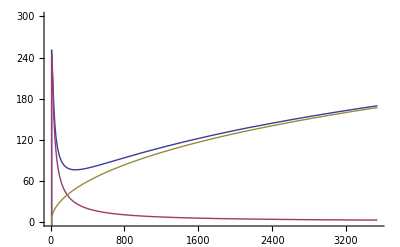

```mathematica
gr1=ListPlot[{datadEdxtotvsE,datadEdxivsE,datadEdxevsE},Joined-> True,PlotRange-> {0,0.3*10^3}]
```

### interpolating functions for dE/dx

```mathematica
dEdxE=Interpolation[datadEdxtotvsE];
dEdxiE=Interpolation[datadEdxivsE];
dEdxeE=Interpolation[datadEdxevsE];
```

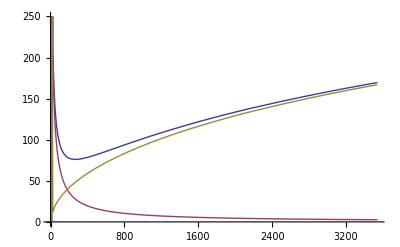

```mathematica
gr2=Plot[{dEdxE[EE],dEdxiE[EE],dEdxeE[EE]},{EE,0,E0},PlotRange-> {0,0.25*10^3}]
```

```mathematica
(* Show[gr1,gr2] *)
```